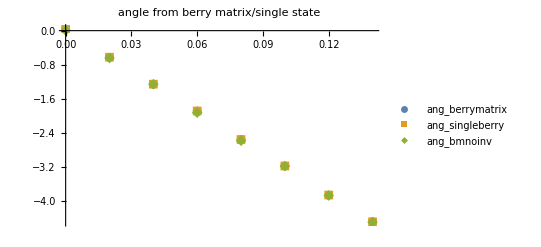

```mathematica
(*
running in the cluster:ne=10,1000 1000 20 1
taking inverse/no inverse/single state plot.
*)
bm=Import["Google Drive/jie_programs/QHlattice/bp/may27_berymatrix","Table"];
bmnoinv=Import["Google Drive/jie_programs/QHlattice/bp/may27_berymatrix_noinv","Table"];
bmsingle=Import["Google Drive/jie_programs/QHlattice/bp/may27_singleberry","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
bm1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
bmnoinv1= Table[{x[[i]],bmnoinv[[i]][[2]]},{i,1,n}];
bmsingle1= Table[{x[[i]],bmsingle[[i]][[2]]},{i,1,n}];

ListPlot[{bm1,bmnoinv1,bmsingle1},PlotLegends->{"ang_berrymatrix","ang_singleberry", "ang_bmnoinv"},PlotMarkers->Automatic, PlotLabel->"angle from berry matrix/single state"]
```